```mathematica
dataDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data"}]
```

/Users/christopher/Dropbox/brown/2019/asyrScience/finalProject/data

```mathematica
translations=Import[FileNameJoin[{dataDirectory,"MX","translations.mx"}]];
```

### Basic Analysis

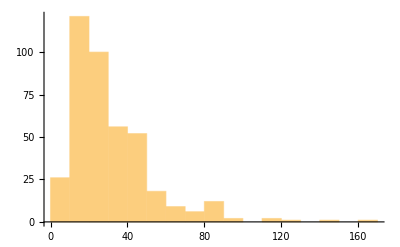

```mathematica
Histogram[Length/@translations]
```

```mathematica
fullText=StringRiffle[StringRiffle[#," ... "]&/@Flatten[Values@translations[[All,All,"Fragments"]],2],"\n"];
```

```mathematica
allFragments=Flatten@Values@translations[[All,All,"Fragments"]];
```

```mathematica
AssociationMap[Total@StringCount[allFragments,#,IgnoreCase->True]&,{"Moon","Mars","Jupiter","Saturn","Venus","Mercury"}]
```

<|Moon→9012,Mars→940,Jupiter→877,Saturn→794,Venus→1236,Mercury→1026|>

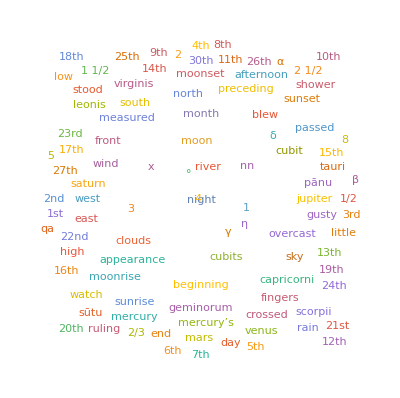

```mathematica
WordCloud@DeleteStopwords@ToLowerCase@Flatten@TextWords@allFragments
```

```mathematica
Counts@Flatten[StringCases[allFragments," "~~d:Shortest[Except[WhitespaceCharacter]..]~~" wind blew":>d,IgnoreCase->True]]
```

<|north→1403,west→58,south→375,east→49,???→1,north?→27,gusty→3,south?→7,west?→3,east?→1|>

```mathematica
allFragments
```

{Month II, the 1st of which was identical with the 30th of the preceding month, sunset to moonset: 12°,Night of the 8th, first part of the night, Mercury was,above η Geminorum,Night of the 11th, beginning of the night, the moon was,in front of α Virginis,16681,Night of the 17th, last part of the night, the moon was 1/2 cubit above β Scorpii, the moon having passed a little to the east, it stood 1 cubit 4 fingers behind Mars to the east,blew?. Night of the 19th, the south wind blew; last part of the night, the moon stood,in front of Saturn to the west,clouds were in the sky, the sun was surrounded by a halo,(illegible traces)}
 |  |  |  |

```mathematica
Import[FileNameJoin[{dataDirectory,"adsd","adsd1","adart1","catalogue.json"}],"RawJSON"]["members"]
```

<|X102611→<|langs→0x08000000,project→adsd/adart1,id_text→X102611,designation→AD -261A,copy→LBAT 249,photo→ADART I plate 66,11,provenience→Babylon,pleiades_id→893951,pleiades_coord→[44.422236,32.543395],supergenre→unknown,trans→{en}|>,415,X301633→<|1|>|>
 |  |  |  |

```mathematica
ReverseSort[Length/@translations][[;;10]]
```

<|X301323→162,X301051→147,X103661→128,X102770→118,X301081→113,X301191→95,X301322→92,X301403→89,X301181→89,X300771→87|>

```mathematica
Sort[Length/@translations][[;;10]]
```

<|X201834→2,X201702→4,X201751→5,X102990→7,X103020→7,X103223→7,X201704→7,X300760→7,X301541→7,X102832→8|>

```mathematica
translations["X102732"][[14]]
```

<|Line→(o 13),Fragments→{{Month VIII, the 1st of which was identical with the 30th of the preceding month,,clouds, I did not see the moon. Night of the 1st, very overcast, rain shower. The 1st, Venus’ last appearance in the west in the end of Scorpius expected; clouds, I did not watch; all day overcast, rain DUL. Night of the 2nd and the 2nd, very overcast, rain DUL. Night of the 3rd, clouds were in the sky. Night of the 4th, beginning of the night, the moon was}}|>

```mathematica
ToLowerCase@TextWords@allFragments;
```

$Aborted